```mathematica
Subscript[J, m_][x_]=BesselJ[m,x]
```

mx

```mathematica
Subscript[j, m_,n_]=BesselJZero[m,n]
```

mn

```mathematica
IP[u_,v_]:=Integrate[x u v,{x,0,1}]
```

## Bessel function of order zero

```mathematica
Series[Subscript[J, 0][x],{x,0,10}]
```

1-x^2/4+x^4/64-x^6/2304+x^8/147456-x^10/14745600+O(x^11)

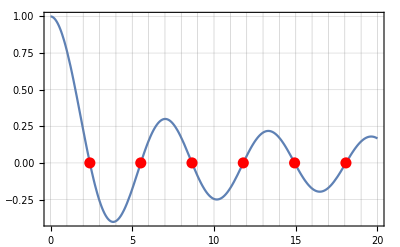

```mathematica
Plot[Subscript[J, 0][x],{x,0,20},GridLines->{Table[i,{i,0,20}],Automatic},Epilog->{PointSize[0.02],Red,Table[Point[{BesselJZero[0,n],0}],{n,1,6}]}]
```

```mathematica
Table[{n,Subscript[j, 0,n],N[Subscript[j, 0,n]]},{n,1,6}]
```

(1 | 01 | 2.40483
2 | 02 | 5.52008
3 | 03 | 8.65373
4 | 04 | 11.7915
5 | 05 | 14.9309
6 | 06 | 18.0711)

```mathematica
IP[Subscript[J, 0][Subscript[j, 0,n] x],Subscript[J, 0][Subscript[j, 0,n] x]]
```

1/2 ((00n)^2+(10n)^2)

## Bessel function of different orders

```mathematica
Series[Subscript[J, 1][x],{x,0,10}]
```

x/2-x^3/16+x^5/384-x^7/18432+x^9/1474560+O(x^11)

```mathematica
Series[Subscript[J, 2][x],{x,0,10}]
```

x^2/8-x^4/96+x^6/3072-x^8/184320+x^10/17694720+O(x^11)

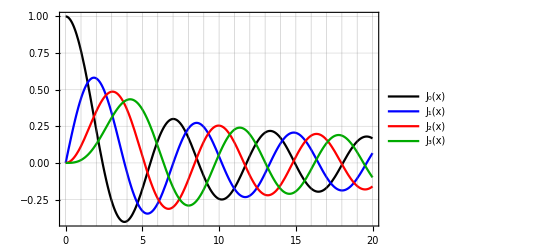

```mathematica
Plot[{Subscript[J, 0][x],Subscript[J, 1][x],Subscript[J, 2][x],Subscript[J, 3][x]},{x,0,20},GridLines->{Table[i,{i,0,20}],Automatic},PlotStyle->{Black,Blue,Red,Darker[Green]},PlotLegends->"Expressions"]
```

```mathematica
Table[{n,Subscript[j, 1,n],N[Subscript[j, 1,n]]},{n,1,6}]
```

(1 | 11 | 3.83171
2 | 12 | 7.01559
3 | 13 | 10.1735
4 | 14 | 13.3237
5 | 15 | 16.4706
6 | 16 | 19.6159)

```mathematica
Table[{n,Subscript[j, 2,n],N[Subscript[j, 2,n]]},{n,1,6}]
```

(1 | 21 | 5.13562
2 | 22 | 8.41724
3 | 23 | 11.6198
4 | 24 | 14.796
5 | 25 | 17.9598
6 | 26 | 21.117)

```mathematica
Assuming[{m∈Integers,n∈Integers},IP[Subscript[J, m][Subscript[j, m,n] x],Subscript[J, m][Subscript[j, m,n] x]]]
```

ConditionalExpression[1/2 (mmn^2-(2 m m+1mn mmn)/mn+(m+1mn)^2), m>-1]

## Standing waves on a disk

```mathematica
Subscript[v, m_,n_][r_,θ_]=Subscript[J, m][Subscript[j, m,n] r]Cos[m θ]
```

cos(θ m) mr mn

```mathematica
showMode[m_,n_]:=Module[{k=N[Subscript[j, m,n]]},RevolutionPlot3D[Subscript[J, m][k r]Cos[m θ],{r,0,1},{θ,0,2Pi},PlotPoints->128]]
```

```mathematica
showMode[0,1]
```

-Graphics3D-

```mathematica
showMode[0,2]
```

-Graphics3D-

```mathematica
showMode[0,3]
```

-Graphics3D-

```mathematica
showMode[0,6]
```

-Graphics3D-

```mathematica
showMode[1,3]
```

-Graphics3D-

```mathematica
showMode[2,5]
```

-Graphics3D-